# Experimental Infra Bundles

[[ LLM Generated ]]

We separate particular finite models from questions about observation at scale and possible limits. The exact statements below concern finite graphs, quotient maps and selected matchings. The completion and emergence section states research requirements; it supplies no general convergence theorem or new scale API. The general definitions are in Infra Bundlespaclet:WolframInstitute/InfraGeometry/tutorial/InfraBundles.

## Setup

```mathematica
Needs[ "WolframInstitute`InfraGeometry`" ]
```

## Particular geometric models

The model names describe how their total vertices and edges are constructed. Their fibration and bundle properties must be checked on the chosen substrate and scale. The name of a model does not assert the general graph-bundle predicate.

| Construction | Total vertices and projection
       | InfraTangentBundle[g,r] | Geodesic rays of length r, projected to their initial vertex
       | InfraCotangentBundle[g,r] | Reversed rays, projected to their terminal vertex
       | InfraDisplacementBundle[g,r] | Pairs of vertices at distance r, projected to the first vertex
       | InfraBundleMorphism | Particular endpoint, truncation and reversal maps between these models
       | InfraFiberedSubstrate | A finite catalogue of products, coverings, branched examples and geometric models

The tangent and cotangent models use adjacency or equality at each position of a ray. The displacement model uses this rule on the two entries of a pair. Their vertical graphs and transverse multiplicities depend on the substrate. Materializing a construction gives an ordinary literal fibered graph for the general readers. Supported models also have explicit predicate methods that materialize once, so manual conversion is optional.

The same cycle supports two ray models and a displacement model.

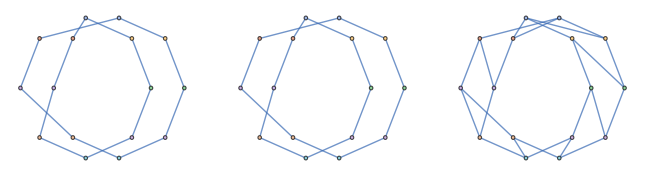

```mathematica
SeedRandom[ 7 ];
With[ { graph = CycleGraph[ 8 ] },
  GraphicsRow[ Map[ model |-> InfraFiberedGraphHighlight[ InfraFiberedGraph[ model ] ],
    { InfraTangentBundle[ graph, 2 ], InfraCotangentBundle[ graph, 2 ], InfraDisplacementBundle[ graph, 1 ] } ] ] ]
```

Metric-selected Levi-Civita constructions can retain partial matchings. A partial result need not satisfy the complete-connection predicate of the general framework. The model-specific transport overload omits blocked starting points; this differs from transport by a complete connection, which is a total fiber bijection.

The legacy random generator remains available with its earlier vertical-count options and cyclic-width horizontal rule. It is a compatibility model, not the property-constrained generator used in the foundation tutorial.

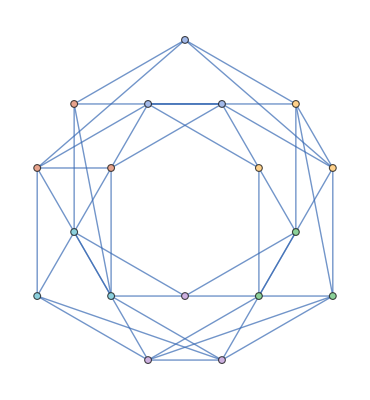

```mathematica
SeedRandom[ 7 ];
With[ { fib = RandomInfraFibration[ CycleGraph[ 6 ], "VerticalVertices" -> 3,
    "VerticalEdges" -> 1, "HorizontalEdgesDensity" -> 1.5 ] },
  InfraFiberedGraphHighlight[ fib ] ]
```

## Exact finite observations at scale

An observation rule must specify what becomes visible at a chosen scale. Balls, powers, covers and partitions perform different operations. None is selected by the inert fibered-graph object itself.

| Choice | Finite operation | Data that must be supplied
       | Metric neighbourhood | Closed graph-distance balls or an existing ball-topology construction | The metric graph and radius
       | Reachability at a scale | Graph power, joining distinct vertices within the chosen distance | Which graph is powered and the integer scale
       | Identifying indistinguishable states | A vertex partition and its reconstructed quotient graph | The partition or observation map
       | A cover-based topology | A nerve or Cech construction | The cover, intersections and scale convention

These operations need not commute with projection. They need not preserve unique lifting, fiber sizes, selected connections or monodromy. Such preservation is a statement to prove for a specified operation.

For example, replace the total graph of the double covering of a square by its second graph power while keeping its vertex projection. A total vertex now has two neighbours over the opposite square vertex. The reconstructed base gains diagonals, and unique lifting fails. The three pictures use reachability scales one, two and three.

```mathematica
SeedRandom[ 7 ];
GraphicsRow[ Map[ radius |-> With[
  { fib = InfraFiberedGraph[ GraphPower[ CycleGraph[ 8 ], radius ], vertex |-> Mod[ vertex, 4, 1 ] ] },
  InfraFiberedGraphHighlight[ fib, { InfraFiber[ fib, 1 ] } ] ], Range[ 3 ] ] ]
```

-Graphics-

## Exact ball projection under weak lifting

Weak edge lifting has a positive consequence at every finite distance scale. Write B_E(x,r) and B_B(p,r) for closed graph-distance balls of integer radius r≥0. A fibered graph has weak edge lifting exactly when

π(B_E(x,r))=B_B(π(x),r)

for every total vertex x and every such radius. It is enough to test radius one.

Every total edge projects to a base edge or a vertex. Projecting a total walk therefore gives a base walk after repetitions are removed, without increasing length. This proves the inclusion from left to right. For the reverse inclusion, choose a shortest base walk from π(x) to a point of its radius-r ball. Weak lifting supplies a transverse lift of each successive step, starting at x. The lifted endpoint lies in the total radius-r ball and projects to the required point. Conversely, equality at radius one supplies a total neighbour over every base neighbour, because a distinct base vertex cannot be the projection of x itself. This is precisely weak edge lifting.

The total ball below projects onto the marked base ball. The statement permits multiple lifts and unequal fibers.

```mathematica
SeedRandom[ 7 ];
With[ { fib = RandomInfraFiberedGraph[ PathGraph[ Range[ 6 ] ], Properties -> { "Fibration" },
    "VerticalVertexCount" -> { 2, 3 }, "HorizontalEdgeCount" -> All ] },
  { total = InfraTotalSpace[ fib ], base = InfraBaseSpace[ fib ] },
  { start = First @ VertexList[ total ] },
  { point = Lookup[ InfraProjection[ fib ], Key[ start ] ] },
  GraphicsRow[ { InfraFiberedGraphHighlight[ fib, { NeighborhoodGraph[ total, start, 2 ] } ],
    InfraSubstrateHighlight[ base, { NeighborhoodGraph[ base, point, 2 ] } ] } ] ]
```

-Graphics-

## Exact reduction by observations

An observation map groups total vertices into classes and thereby defines another reconstructed base. This quotient records whether some edge joins two classes. It does not retain how many lifts each representative has. The multiplicity measurement reads that information before reduction.

Here adjacent pairs of vertices of a cycle become single observed states. Each fiber is an edge, but its two endpoints lift different directions of the quotient cycle. This is a valid fibered graph without the weak fibration property.

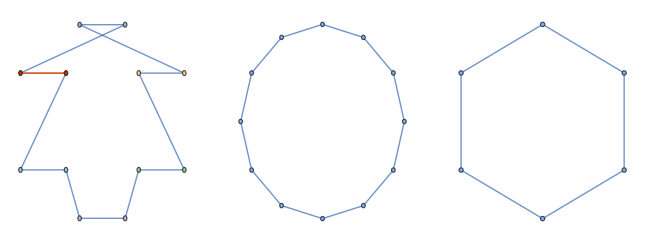

```mathematica
SeedRandom[ 7 ];
With[ { fib = InfraFiberedGraph[ CycleGraph[ 12 ], vertex |-> Ceiling[ vertex / 2 ] ] },
  GraphicsRow[ { InfraFiberedGraphHighlight[ fib, { InfraFiber[ fib, 1 ] } ],
    InfraTotalSpace[ fib ], InfraBaseSpace[ fib ] } ] ]
```

There is an exact criterion for reducing a projection. Let α:V(E)→OverBar[V(E)] and β:V(B)→OverBar[V(B)] describe total and base observations. A map π̄ satisfying

π̄∘α=β∘π

exists exactly when β(π(x))=β(π(y)) whenever α(x)=α(y). Necessity follows by applying the displayed identity to both representatives. For sufficiency, define π̄(α(x))=β(π(x)); the condition makes this independent of the representative. With quotient adjacency reconstructed from edges, each edge still projects to an edge or a vertex. This establishes a reduced graph map, without establishing any lifting property.

## Exact descent of a selected transport

Suppose a complete connection transports F_p to F_q by a bijection T_pq. Choose an equivalence relation in each fiber. The transport descends to a map of equivalence classes exactly when

x∼_p y  ⟹  T_pq(x)∼_q T_pq(y).

Indeed, this condition says precisely that the proposed image class is independent of the representative. The descended map is a bijection with descended inverse when the same condition holds for T_pq^-1. If the original transport is a fiber-graph isomorphism, these two conditions also give an isomorphism of the reconstructed quotient fiber graphs. Every original adjacency maps to a quotient adjacency or a collapsed vertex, and the inverse gives the converse.

These conditions can be checked for a proposed observation. An arbitrary partition need not satisfy them. Merging base vertices creates additional compatibility questions and is not covered by this fixed-base descent statement.

## Proposed completion and emergence questions

A single finite unweighted graph does not determine a continuum limit. A completion claim needs a family of finite objects, scale choices and a specified notion of convergence. A bundle-emergence claim additionally needs a limit projection and a stated bundle class.

The following are research requirements to formulate and prove in a chosen model, not a sufficient-condition theorem.

Specify total graphs, base graphs and projections at each resolution, together with the comparison maps between resolutions.

Specify how graph distance is rescaled and what convergence of total spaces, base spaces and projections means.

Control the fibers under those comparisons. Equal cardinalities at one resolution neither prevent collapse nor produce a limiting fiber topology.

Construct compatible local identifications and prove the limit's required local product or lifting property.

If connections are retained, specify a common transport target or compatible actions, and prove convergence of transport along comparable walks.

If curvature is claimed, supply faces or another loop family and prove the appropriate scaled holonomy statement.

There is a basic exact obstruction to retaining a nontrivial fiber under uniform metric rescaling. Suppose every vertical fiber is a copy of one fixed connected graph F of diameter D. When every total edge has rescaled length a_n, two vertices in the same fiber have total-space distance at most a_n D, using a vertical path. If a_n tends to zero, all such pairwise fiber distances tend to zero. Thus a proposed nontrivial limiting fiber needs additional structure or a different scaling regime.

A graph-bundle predicate alone supplies none of these limiting choices. Even geometric realization requires care: a Cartesian product graph contains edges, but no filled squares. The local product requirement for topological bundles concerns spaces and their neighbourhoods, as in Hatcher, Algebraic Topology, Section 4.2.

Finite models motivated by the seven-sphere, Hurwitz algebras or Hopf fibrations belong to particular research constructions. Each needs its own projection, algebraic action and comparison with the intended continuous object. They are not assumptions of the finite framework, and do not establish generic emergence of topological bundles.

## Holonomy under changed fiber coordinates

There is an exact statement before any limiting argument. If fiber coordinates are changed by bijections g_p, edge transport becomes g_q T_pq g_p^-1. Around a closed walk at p, intermediate coordinate changes cancel, so holonomy becomes g_p H g_p^-1. Its conjugacy class is therefore independent of those coordinate choices. If the coordinates and transport are required to preserve fiber graphs, the bijections must be graph isomorphisms.

This is the finite gauge interpretation in Ioana Milea's Fibered Graph Gauge Theory Basics, unpublished, 2026. It does not supply a face system or a continuum limit. The general holonomy reader remains a permutation of one finite fiber, and the retained flat-connection predicate remains the test of trivial global monodromy.

Related Guides

InfraFiberBundlespaclet:WolframInstitute/InfraGeometry/guide/InfraFiberBundles ▪ Experimentalpaclet:WolframInstitute/InfraGeometry/guide/Experimental ▪ InfraTopologypaclet:WolframInstitute/InfraGeometry/guide/InfraTopology

Related Tech Notes

InfraBundlespaclet:WolframInstitute/InfraGeometry/tutorial/InfraBundles

## Metadata

### Categorization

Tutorial

WolframInstitute/InfraGeometry

WolframInstitute`InfraGeometry`

WolframInstitute/InfraGeometry/tutorial/ExperimentalInfraBundles

### Keywords

experimental

fibered graph

scale

observation

reduction

completion

emergence

tangent bundle

displacement bundle